```mathematica
ClearAll["Global`*"];
R1=RotationMatrix[-ψ[s],{0,0,1}];
R2=RotationMatrix[-θ[s],{0,1,0}];
R3=RotationMatrix[-ϕ[s],{1,0,0}];
Fvec=R3.R2.R1.{F,0,0};
d1=FullSimplify[Inverse[R3.R2.R1].{1,0,0}];
d2=FullSimplify[Inverse[R3.R2.R1].{0,1,0}];
d3=FullSimplify[Inverse[R3.R2.R1].{0,0,1}];
kn={-1/R,0,0};
k={ϕ'[s]-Sin[θ[s]]*ψ'[s],θ'[s]*Cos[ϕ[s]]+Cos[θ[s]]*Sin[ϕ[s]]*ψ'[s],-Sin[ϕ[s]]*θ'[s]+Cos[θ[s]]*Cos[ϕ[s]]*ψ'[s]};
{M1,M2,T}=B*{{1,0,0},{0,1,0},{0,0,RR}}.(k-kn);
Mvec={M1,M2,T} ;
Expand[D[Mvec,s]]//MatrixForm;
crss=FullSimplify[{{k[[2]]*Mvec[[3]]-k[[3]]*Mvec[[2]]},{k[[3]]*Mvec[[1]]-k[[1]]*Mvec[[3]]},{k[[1]]*Mvec[[2]]-k[[2]]*Mvec[[1]]}}];
eqns=FullSimplify[Thread[D[Mvec,s]+crss=={{Fvec[[2]]},{-Fvec[[1]]},{0}}]/. R->1/. B->8000./. RR->2/3];
H=FullSimplify[{{-Sin[θ[s]],0,1},{Cos[θ[s]]*Sin[ϕ[s]],Cos[θ[s]],0},{RR*Cos[θ[s]]*Cos[ϕ[s]],-RR*Sin[ϕ[s]],0}}/. R->1/. B->8000./. RR->2/3];
```

```mathematica
startpt=0.01;
startval=0.001;
endpt=2Pi;
IC1=ψ[startpt]==startval;
IC2=θ[startpt]==startval;
IC3=ϕ[startpt]==startval;
IC5=FullSimplify[Part[k,1]-Part[kn,1]]==startval/. s->endpt/. R->1;
IC4=FullSimplify[Part[k,2]-Part[kn,2]]==startval/. s->endpt/. R->1;
IC6=FullSimplify[Part[k,3]-Part[kn,3]]==startval/. s->endpt/. R->1;
bcs={IC1,IC2,IC3,IC4,IC5,IC6};
solution=Block[{F=512},NDSolve[Join[eqns,bcs],{ψ[s],θ[s],ϕ[s]},{s,startpt,endpt},Method->"BoundaryValues"->{"Shooting","StartingInitialConditions"->{ψ'[startpt]==1.,θ'[startpt]==1.,ϕ'[startpt]==1.}}]];
```

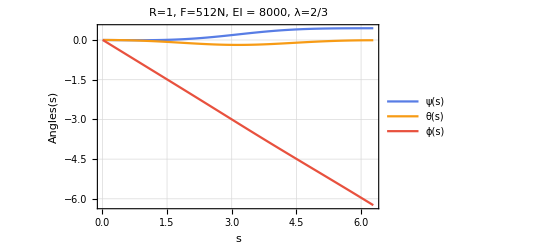

```mathematica
Plot[Evaluate[{ψ[s],θ[s],ϕ[s]}/.solution ],{s,0.01,2*Pi},
PlotTheme->{"BoldColors","Frame","Grid"},
FrameLabel->{s,Angles[s]},
FrameStyle->Directive[16,Black],PlotLegends->{ψ[s],θ[s],ϕ[s]},
PlotLabel->Style[Framed["R=1, F=512N, EI = 8000, λ=2/3"]]]
```

```mathematica
dyds=d3/.solution;
fn[z_?NumericQ]:=NIntegrate[dyds,{s,startpt,z}];
fn[2Pi*R]/.R->1
```

{{1.00122,0.173959,0.00416271}}

```mathematica
ParametricPlot3D[{fn[y]⟦1,1⟧,fn[y][[1,2]],fn[y]⟦1,3⟧},{y,0.01,2 π*1}]
```

-Graphics3D-